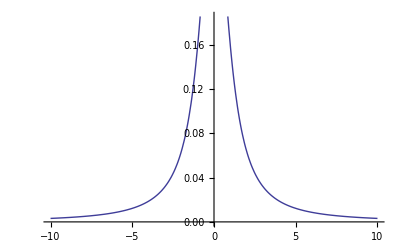

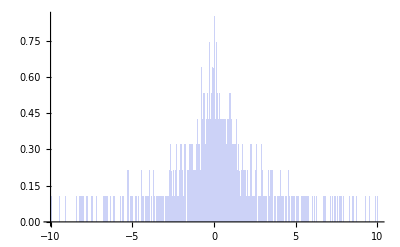

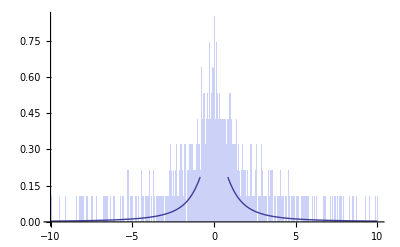

```mathematica
px[x_]:=1/(√(2π))Exp[(-(x)^2)/2];
py[y_]:=1/(√(2π))Exp[(-(y)^2)/2];
p1=Plot[∫_(-∞)^∞ Abs[y]px[y z]py[y]ⅆy,{z,-10,10}]
xi=RandomVariate[NormalDistribution[0,1],10^3];
yi=RandomVariate[NormalDistribution[0,1],10^3];
zi=xi/yi;
p2=Histogram[zi,{-10,10,0.01},"PDF"]
Show[p2,p1,PlotRange->All]
```

```mathematica
px[x_]:=1/(√(2π))Exp[(-(x)^2)/2];
py[y_]:=1/(√(2π))Exp[(-(y)^2)/2];
∫_(-∞)^∞ Abs[y]px[y z]py[y]ⅆy
```

ConditionalExpression[1/(π (1+z^2)),Re[z^2]>-1]

```mathematica
px[x_]:=Exp[-x];
py[y_]:=Exp[-y];
∫_0^∞ Abs[y]px[y z]py[y]ⅆy
```

Piecewise[{{1/(1+z)^2, Re[z]>-1}, {Integrate[ⅇ^(-y-y z) Abs[y],{y,0,∞},Assumptions→Re[z]≤-1], True}}]

```mathematica
px[x_]:=PDF[ChiSquareDistribution[2],x]
px[y_]:=PDF[ChiSquareDistribution[2],y]
∫_0^∞ y px[y z]py[y]ⅆy
```

Piecewise[{{2/(2+z)^2, z>0}, {0, True}}]

ClearAll

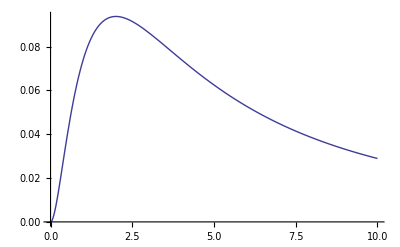

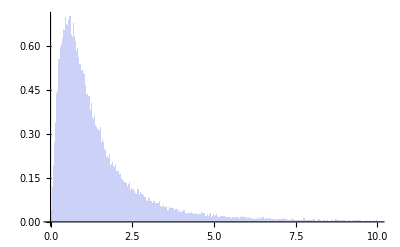

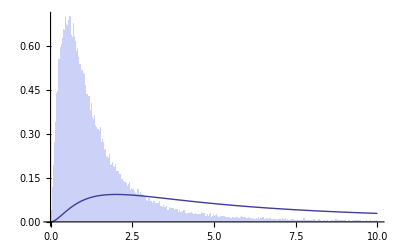

```mathematica
ClearAll
px[x_]:=PDF[ChiSquareDistribution[6],x]
px[y_]:=PDF[ChiSquareDistribution[6],y]
p1=Plot[∫_0^∞ y px[y z]py[y]ⅆy,{z,0,10}]
xi=RandomVariate[ChiSquareDistribution[6],10^5];
yi=RandomVariate[ChiSquareDistribution[6],10^5];
zi=xi/yi;
p2=Histogram[zi,{0,10,0.01},"PDF"]
Show[p2,p1,PlotRange->All]
```

ClearAll

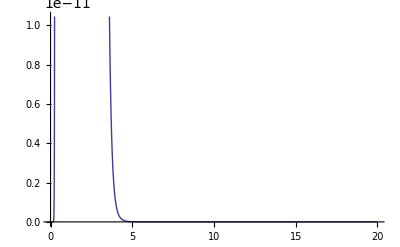

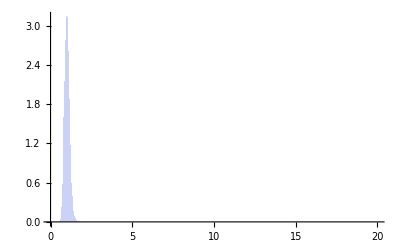

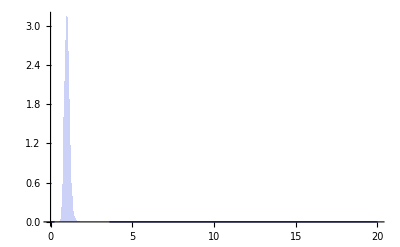

```mathematica
ClearAll
px[x_]:=PDF[NormalDistribution[10,1],x]
py[y_]:=PDF[NormalDistribution[10,1],y]
p1=Plot[∫_(-∞)^∞ Abs[y]px[y z]py[y]ⅆy,{z,0,20}]
xi=RandomVariate[NormalDistribution[10,1],10^4];
yi=RandomVariate[NormalDistribution[10,1],10^4];
zi=xi/yi;
p2=Histogram[zi,{0,20,0.01},"PDF"]
Show[p2,p1,PlotRange->All]
```